## EWS for stationary simulations of the Ricker model (no seasonality)

## Import data

### EWS data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/ricker_std"];
```

```mathematica
(* raw EWS data *)
ewsX=Import["data_export/ews_stat/ews.csv"];
```

### Bifurcation data

```mathematica
bifPtsX=Import["data_export/bif_data_ricker.csv"];
```

```mathematica
(* clear out points that go beyond max dilution rate on plot *)
bifPtsX=Table[DeleteCases[bifPtsX[[i]],{x_,_}/;x>1.5],{i,1,Length[bifPtsX]}];
```

```mathematica
(* bifurcation points (from MMA bif file) *)
bif1=2;
```

### General figure parameters

```mathematica
(* plot range for r *)
xRange={0.5,4};
```

```mathematica
imgs=500;
aRatio=0.3;
padding={{60,60},{20,20}};
{{padLeft,padRight},{padBottom,padTop}}=padding;
lt=0.006;
colX=Darker[TMBcolours[[1]],0.2];
colY=Darker[TMBcolours[[4]],0.2];
{colX,colY}
labelPos=Scaled[{0.03,0.85}];
```

{RGBColor[0.2947336, 0.4054232, 0.5678384000000001],RGBColor[0.7380207999999999, 0.3085008, 0.1673432]}

```mathematica
rVals=Union[ewsX[[2;;,1]]];
rMax=Max[rVals];
```

## Bifurcation diagram

```mathematica
(* figure parameters *)
pSize = 0.0025;
yRangeBif = {0,700};
```

### Population post-breeding period

```mathematica
(* Extract growth (r) values and state values *)
rValsX=bifPtsX[[1,2;;]];
stateValsX=bifPtsX[[2;;,2;;]];
```

```mathematica
(* Normalise state values by carrying capacity (plot x/k) *)
stateValsNormX=stateValsX/kb;
```

```mathematica
(* Arrange for plotting *)
plotValsX=Table[Transpose[{rValsX,stateValsX[[i]]}],{i,1,Length[stateValsX]}];
```

```mathematica
bifRickerX=ListPlot[plotValsX[[1;;5]],
Frame->True,
FrameLabel->{{"Population size",None},{"Growth rate (r_b)",None}},
FrameStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
PlotRange->{xRange,yRangeBif},
PlotStyle->Directive[{colX,PointSize[pSize]}],
AspectRatio->aRatio,
ImageSize->imgs,
LabelStyle->14,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["a",14,Bold],labelPos]}];
```

### Combine bifurcation plots

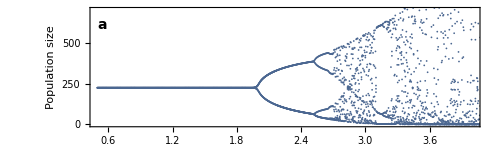

```mathematica
bifPlot=Show[bifRickerX]
```

## Plots of EWS against delta

```mathematica
(* Columns of DataFrame *)
ewsX[[1]]
```

{Growth rate,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax,Smax/Var}

### Variance

```mathematica
index=Position[ewsX[[1]],"Variance"][[1,1]];
```

```mathematica
varX=ewsX[[2;;,index]];
varY=ewsY[[2;;,index]];
```

```mathematica
rVals//Dimensions
```

{100}

```mathematica
powersRangeX=Range[-4,4,2];
powersRangeY=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange1}],Table[Superscript["10",ToString[i]],{i,powersRangeX}]}];
yTicksY=Transpose[{Table[10^i,{i,powersRange2}],Table[Superscript["10",ToString[i]],{i,powersRangeY}]}];
```

```mathematica
varPlot=ListLogPlot[Transpose[{rVals,varX}],
LabelStyle->14,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{yTicksX,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",14,Bold],labelPos]}
];
```

### Coefficient of variation

```mathematica
index=Position[ewsX[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
cvarX=ewsX[[2;;,index]];
```

```mathematica
cvarPlot=ListLogPlot[Transpose[{rVals,cvarX}],
LabelStyle->14,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"C.V.",""},{"",""}},
FrameTicks->{{{{10^(-3),"10^-3"},{10^(-2),"10^-2"},{10^(-1),"10^-1"},{1,1},{10,10}},None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}];
```

### Lag-1 AC

```mathematica
index=Position[ewsX[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
acX=ewsX[[2;;,index]];
```

```mathematica
acPlot=ListLinePlot[Transpose[{rVals,acX}],
LabelStyle->14,
PlotRange->{xRange,{-1.1,1.1}},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Lag-1 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",14,Bold],labelPos]}];
```

### Lag-2 AC

```mathematica
index=Position[ewsX[[1]],"Lag-2 AC"][[1,1]];
```

```mathematica
acX=ewsX[[2;;,index]];
```

```mathematica
ac2Plot=ListLinePlot[Transpose[{rVals,acX}],
LabelStyle->14,
PlotRange->{xRange,{-1.1,1.1}},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Lag-2 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",14,Bold],labelPos]}];
```

### Lag-3 AC

```mathematica
index=Position[ewsX[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
acX=ewsX[[2;;,index]];
```

```mathematica
ac3Plot=ListLinePlot[Transpose[{rVals,acX}],
LabelStyle->14,
PlotRange->{xRange,{-1.1,1.1}},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Lag-3 AC",""},{"",""}},
FrameTicks->{{Range[-1,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["e",14,Bold],labelPos]}];
```

### Smax

```mathematica
index=Position[ewsX[[1]],"Smax"][[1,1]];
```

```mathematica
smaxX=ewsX[[2;;,index]];
```

```mathematica
powersRangeX=Range[-4,4,2];
powersRangeY=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange1}],Table[Superscript["10",ToString[i]],{i,powersRangeX}]}];
yTicksY=Transpose[{Table[10^i,{i,powersRange2}],Table[Superscript["10",ToString[i]],{i,powersRangeY}]}];
```

```mathematica
smaxPlot=ListLogPlot[Transpose[{rVals,smaxX}],
LabelStyle->14,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"S_max",""},{"",""}},
FrameTicks->{{yTicksX,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

### Coherence Factor

```mathematica
index=Position[ewsX[[1]],"Coherence factor"][[1,1]];
```

```mathematica
cfX=ewsX[[2;;,index]];
```

```mathematica
(* Y ticks on log scale *)
powersRangeX=Range[-4,4,2];
powersRangeY=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange1}],Table[Superscript["10",ToString[i]],{i,powersRangeX}]}];
yTicksY=Transpose[{Table[10^i,{i,powersRange2}],Table[Superscript["10",ToString[i]],{i,powersRangeY}]}];
```

```mathematica
cfPlot=ListLogPlot[Transpose[{rVals,cfX}],
LabelStyle->14,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Coherence",""},{"",""}},
FrameTicks->{{yTicksX,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["e",14,Bold],labelPos]}];
```

### AIC weight fold

```mathematica
index=Position[ewsX[[1]],"AIC fold"][[1,1]];
```

```mathematica
aicfoldX=ewsX[[2;;,index]];
```

```mathematica
aicfoldPlot=ListLinePlot[Transpose[{rVals,aicfoldX}],
LabelStyle->14,
PlotRange->{xRange,{-0.1,1.1}},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"w_fold(C)",""},{"",""}},
FrameTicks->{{Range[0,1,0.5],None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->padding];
```

### AIC weight hopf

```mathematica
index=Position[ewsX[[1]],"AIC hopf"][[1,1]];
```

```mathematica
aichopfX=ewsX[[2;;,index]];
```

```mathematica
aichopfPlot=ListLinePlot[Transpose[{rVals,aichopfX}],
LabelStyle->14,
PlotRange->{xRange,{-0.1,1.3}},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"w_hopf",""},{"Growth rate (r_b)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["g",14,Bold],labelPos]}];
```

### AIC weight Null

```mathematica
index=Position[ewsX[[1]],"AIC null"][[1,1]];
```

```mathematica
aicNullX=ewsX[[2;;,index]];
```

```mathematica
aicNullPlot=ListLinePlot[Transpose[{rVals,aicNullX}],
LabelStyle->14,
PlotRange->{xRange,{-0.1,1.2}},
PlotStyle->colX,
Frame->{{True,True},{True,True}},
FrameLabel->{{"w_null(C)",""},{"Growth rate (r_b)",""}},
FrameTicks->{{Range[0,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{colX,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aratio,
ImagePadding->{{padLeft,padRight},{padBottom*1.3,padTop}},
Epilog->{Directive[{Black}],Text[Style["f",14,Bold],labelPos]}];
```

## Grid all plots together

```mathematica
plotTemp=Grid[{{bifPlot},{varPlot},{acPlot},{ac2Plot},{ac3Plot},{smaxPlot},{aichopfPlot}},Spacings->{0,-1.5}];
```

```mathematica
(* Add vertical lines where bifurcations are *)
lHeight1=0.2;
lHeight2=10.5;
lPos=4.32;
l1=Line[{{lPos,lHeight1},{lPos,lHeight2}}];
```

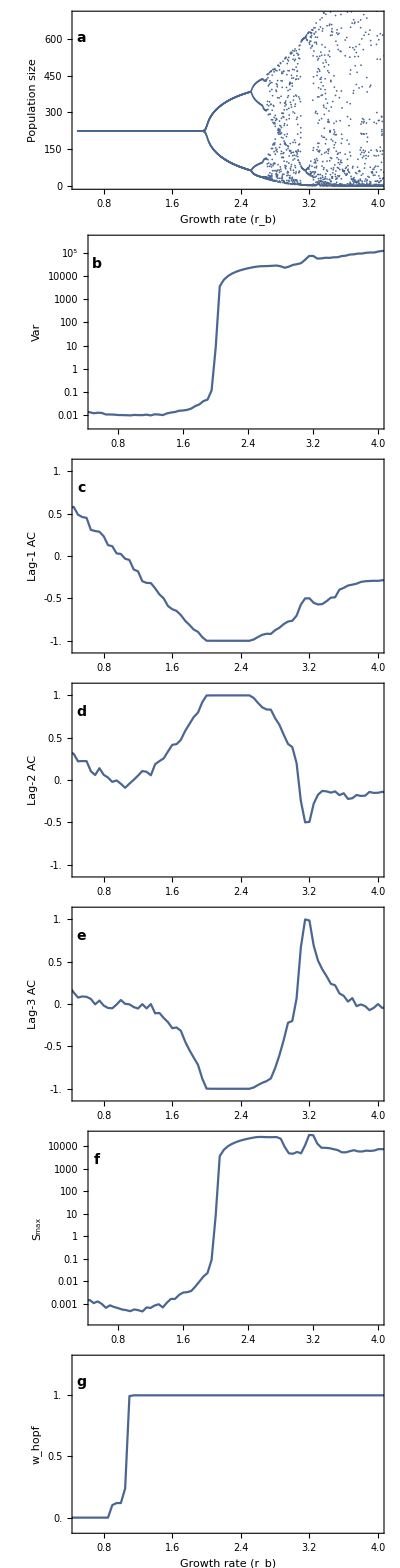
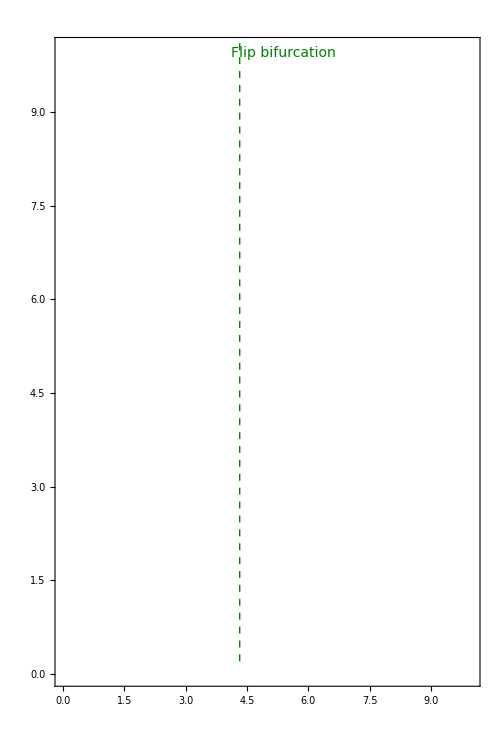

```mathematica
ewsModelPlot=Overlay[{plotTemp,
Graphics[{{Darker[Green,0.5],Dashed,Thickness[0.002],l1},
{Text[Style["Flip bifurcation",14,Darker[Green,0.5]],{5.4,9.95}]}
},
ImageSize->500,AspectRatio->1.5,Frame->True,
FrameStyle->Directive[Opacity[0]],
PlotRange->{{0,10},{0,10}}]
}
]
```

```mathematica
Export["figures/ews_stat_ricker.png",ewsModelPlot,ImageResolution->200];
```